```mathematica
chain={{3,3,3}, {3,3,4}};
```

```mathematica
dimMap={1->{1,0,0},2->{0,1,0},3->{0,0, 1}}
```

{1→{1,0,0},2→{0,1,0},3→{0,0,1}}

```mathematica
chooseDimension[]:=Module[{a=Random[]},
b=If[a<0.333, 1, If[a>0.67, 3, 2]];
b]
```

```mathematica
chooseDimension[]
```

2

```mathematica
addPoint[chain_,box_]:=Module[{lastLink, newLink},
lastLink=Last[chain];
newLink=lastLink+Sign[Random[]-0.5]*(chooseDimension[]/.dimMap);
If[newLink[[1]]≤box && newLink[[1]]≥1 && newLink[[2]]≤box && newLink[[2]]≥1 && newLink[[3]]≤box && newLink[[3]]≥1 ,
If[MemberQ[chain, newLink], chain, Append[chain, newLink]], chain]]
```

```mathematica
(* For some reason this isn't working now *)
generateChain[chain_, box_, iterations_]:=Module[{newChain},
newChain = chain;
For[i=1, i<iterations,i++,
newChain=addPoint[newChain, box];];
newChain
]
```

```mathematica
countItems[list_, item_]:=Length[Select[list, #== item &]]
```

```mathematica
L= 9;
mid=Round[(L+1)/2, 1];
chainLengths={};
For[j=1,j<5000,
chainLengths=Append[chainLengths,Length[generateChain[{{mid,mid,mid}, {mid,mid,mid+1}}, L, L^3]]];
j++];
chainLengths9=chainLengths;
```

```mathematica
data9={#, countItems[Floor[#/2]&/@chainLengths9, #]}&/@Range[220];
```

```mathematica
?Legended
```

RowBox[{"Legended", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["leg", "TI"]}], "]"}] displays StyleBox["expr", "TI"] with legend StyleBox["leg", "TI"]. 
RowBox[{"Legended", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["lbl", "TI"]}], "]"}] indicates in plotting and charting functions that a legend entry for StyleBox["expr", "TI"] should be created, with label StyleBox["lbl", "TI"].

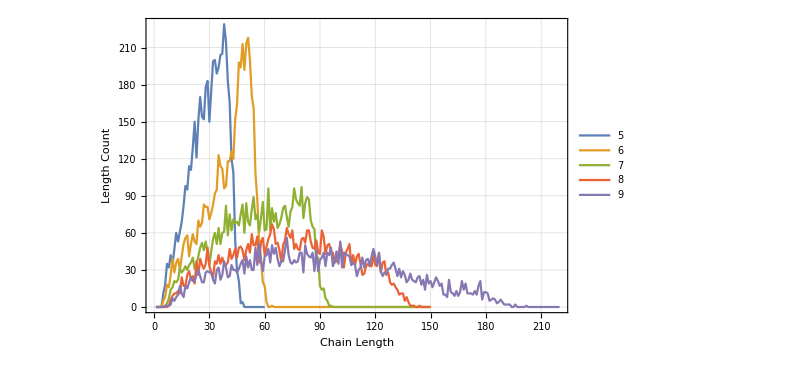

```mathematica
ListPlot[{data5,data6,  data7, data8, data9}, Joined->True, PlotRange->All, Frame->True, ImageSize->600, PlotStyle->Directive[18], GridLines->Automatic,FrameLabel->{"Chain Length", "Length Count"}, PlotLegends->{5,6,7,8,9}]
```

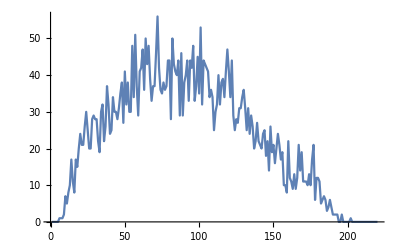

```mathematica
ListPlot[data9, Joined->True, PlotRange->All]
```

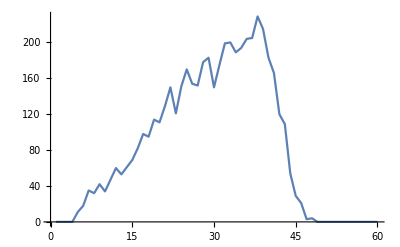

```mathematica
(* Iteresting shape - doesn't look Gaussian or Poisson.  One slope going up, another one going down *)
ListPlot[data5, Joined->True]
```

```mathematica
;
```

```mathematica
visualizeChain[L_]:=Module[{},
mid=Round[(L+1)/2, 1];
chain=generateChain[{{mid,mid,mid}, {mid,mid,mid+1}}, L, 2000];
Graphics3D[{Sphere[#, 0.02]&/@chain, Thick, Line[{chain[[#]], chain[[#+1]]}]&/@Range[Length[chain]-1], Red, Sphere[Last[chain], L/20], Blue, Sphere[#, L/20]&/@{{0, 0, 0}, {L, 0,0}, {L,L, 0}, {L, 0, L}, {L, L,L}, {0, 0, L}, {0, L, 0}, {0, L, L}}}]]
```

```mathematica
visualizeChain[#]&/@{4,5,6,7,8,9, 10, 11}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

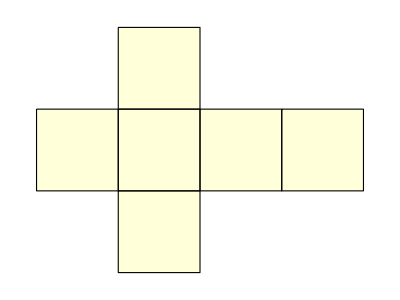
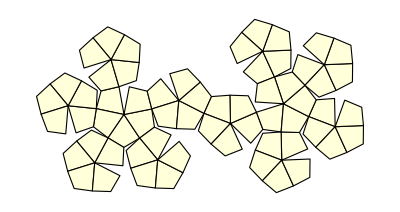
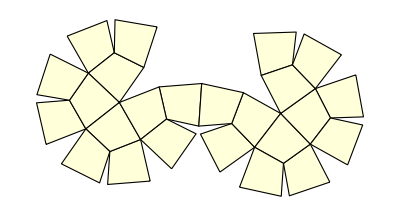
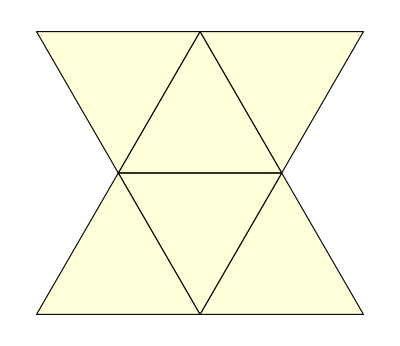
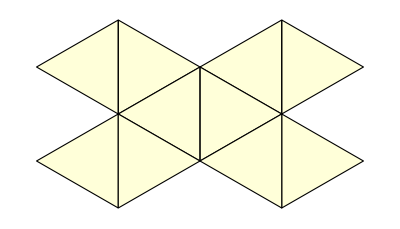
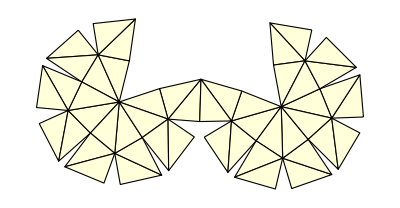
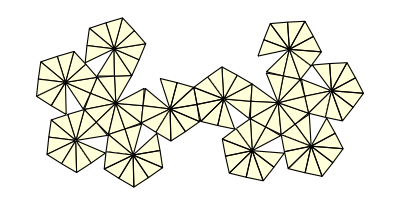
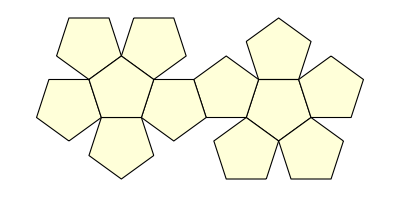
-Graphics3D-
-Graphics-
8
12
Cube | -Graphics3D-
-Graphics-
62
120
DeltoidalHexecontahedron | -Graphics3D-
-Graphics-
26
48
DeltoidalIcositetrahedron | -Graphics3D- | 
-Graphics- | 
5 | 
9 | 
Dipyramid | 3 | -Graphics3D- | 
-Graphics- | 
7 | 
15 | 
Dipyramid | 5
-Graphics3D-
-Graphics-
26
72
DisdyakisDodecahedron | -Graphics3D-
-Graphics-
62
180
DisdyakisTriacontahedron | -Graphics3D-
-Graphics-
20
30
Dodecahedron | -Graphics3D-
-Graphics-
12
30
Icosahedron | -Graphics3D-
-Graphics-
6
12
Octahedron
-Graphics3D-
-Graphics-
92
150
PentagonalHexecontahedron | -Graphics3D-
-Graphics-
38
60
PentagonalIcositetrahedron | -Graphics3D-
-Graphics-
32
90
PentakisDodecahedron | -Graphics3D-
-Graphics-
14
24
RhombicDodecahedron | -Graphics3D-
-Graphics-
32
60
RhombicTriacontahedron
-Graphics3D-
-Graphics-
14
36
SmallTriakisOctahedron | -Graphics3D-
-Graphics-
4
6
Tetrahedron | -Graphics3D-
-Graphics-
14
36
TetrakisHexahedron | -Graphics3D-
-Graphics-
32
90
TriakisIcosahedron | -Graphics3D-
-Graphics-
8
18
TriakisTetrahedron

```mathematica
TableForm[Partition[{Graphics3D[{Opacity[.9],FaceForm[LightGray],PolyhedronData[#,"Faces"]},Lighting->"Neutral"],PolyhedronData[#,"NetImage"],PolyhedronData[#,"VertexCount"],PolyhedronData[#,"EdgeCount"],PolyhedronData[#,"StandardName"]}&/@PolyhedronData["Isohedron"],5]]
```